# Predict the Scale of Satellite Images

Some explanation

Mehmet Sahin, Jun. 26,  2018

Some explanation

## Collect Satellite Images

In this section, we will get the data using GeoImage.

Some explanation

```mathematica
(*ClearAll["Global`*"]*)
```

Create a function to get countries’ geo positions randomly:

```mathematica
geoPositionOfCountry[entities_,numberOfPosition_Integer,folderName_String] :=
	Module[{},
	countries = entities;
	mesh = DiscretizeGraphics@EntityValue[countries,"Polygon"];
	SeedRandom[Hash@{folderName,countries}];
	Reverse[RandomPoint[mesh,numberOfPosition],{2}]
]
```

Let’s plot them and see how those random positions act on a Graphic

```mathematica
trainingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},500,"training"];
validationDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},100,"validation"];
testingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},25,"testing"];

trainingDataOfCities = geoPositionOfCountry[{},500,"training"];
validationDataOfCities = geoPositionOfCountry[{},100,"validation"];
testingDataOfCities = geoPositionOfCountry[{},25,"testing"];

GeoListPlot@GeoPosition@trainingDataOfCountry
GeoListPlot@GeoPosition@trainingDataOfCities
```

-Graphics-

-Graphics-

```mathematica
getZoomLevel[point_] := 
	(SeedRandom[Hash[point]]; normalize[RandomReal[]]);
```

```mathematica
SetAttributes[{getGeoRange, normalize}, Listable]

getGeoRange[zoom_] := zoom * 8800 + 9; (*8800*) (*0.2*)
normalize[number_] := If[number>9,number,number^10]; (*If[number<0.3,number,number^17];*)
```

```mathematica
zoomLevel = getZoomLevel[#]&/@trainingDataOfCities;
geoRange = getGeoRange@getZoomLevel[#]&/@trainingDataOfCities;
```

Check the distribution of points and zoom level:

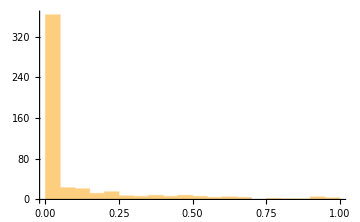

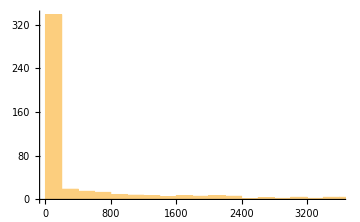

8753.71

-Graphics-

9.

-Graphics-

```mathematica
Histogram@zoomLevel
Histogram@geoRange
Max[geoRange]
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[Max[geoRange],"Miles"],ImageSize->Medium]
minGeoRange =Min[geoRange]
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[minGeoRange,"Miles"],ImageSize->Medium]
```

Create a function to return a association of points and zoom level:

```mathematica
associateThePositionsWithGeoRange[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[#]|>&,points];
```

Combine data:

```mathematica
trainingData = Join[trainingDataOfCountry,trainingDataOfCities];
testingData = Join[testingDataOfCountry,testingDataOfCities];
validationData = Join[validationDataOfCountry,validationDataOfCities];
```

Call the createTheDataSet function:

```mathematica
assocoatedtrainingData = associateThePositionsWithGeoRange[trainingData];
assocoatedvalidationData = associateThePositionsWithGeoRange[validationData];
assocoatedtestingData = associateThePositionsWithGeoRange[testingData];
```

```mathematica
Length@assocoatedvalidationData
Take[assocoatedtrainingData,2]
Take[Dataset@assocoatedtrainingData,2]
```

200

{<|Point→{46.4783,-98.8086},Zoom→0.0316028|>,<|Point→{35.8557,-79.1915},Zoom→2.4521×10^-8|>}

Dataset[<>]

Let’s now write our function that will encode and decode name of the images:

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

Try out the encodeID and decodeID:

```mathematica
Part[assocoatedtrainingData,2]
encodeID[Part[assocoatedtrainingData,2]]
decodeID[%]
```

<|Point→{35.8557,-79.1915},Zoom→2.4521×10^-8|>

ODpBAi1TBVBvaW50wSMBAurcmqKG7UFA5F7RIULMU8AtUwRab29tckIIA0VKVFo+

<|Point→{35.8557,-79.1915},Zoom→2.4521×10^-8|>

### So, far we have created all the needed functions. Now, we will create our new function that takes all the function and creates folder for a image with association name which was encoded. Then, we will part our image into sub images and store them into the folder we created. This will continue for every image we get using GeoImage.

Create a function to getImages from GeoImage:

```mathematica
getImage[coords_List, range_] := 
  	GeoImage[GeoPosition[coords], GeoRange ->range];
```

Before we create our store image function, we should create a hash function to get unique names for images:

```mathematica
(*hash[expr_] := 
	IntegerString[Hash[expr],36];*)
```

Now, let’s create our storeImage function:

```mathematica
ClearAll[imageLocation]
(*imageLocation[zoomLevel_,imageNumber_] := 
	FileNameJoin[{NotebookDirectory[],ToString[zoomLevel]<>"-"<>ToString[imageNumber]<>".png"}];*)
imageLocation[notebookDirectory_,zoomLevel_,imageNumber_] := 
	FileNameJoin[{notebookDirectory,encodeID[ToString[zoomLevel]<>"-"<>ToString[imageNumber]]<>".png"}];
```

Create a function to get folder location with encoded name:

```mathematica
ClearAll[folderLocation]
folderLocation[exp_,trainingOrTestingFolder_] := 
	FileNameJoin[{NotebookDirectory[],"StalliteImages",trainingOrTestingFolder,encodeID[exp]}];
```

### Okey now it is time to create our function to partition images into smaller parts.

```mathematica
(*When images were parted, their zoom level changed. To prevent that, I also converted the zoom leve for each image by simply dividing the real zoom level with the number of images!*)
partitionTheImage[img_,geoRange_,levelOfPartition_] := 
	Table[<|geoRange/n->Flatten@ImagePartition[img,Scaled[1/n]]|>,{n,1,levelOfPartition}];

saveImages[folderName_,partedImage_] :=
	Table[
		Module[{key,values,imglocation},
		key = First[Keys@partedImage];
		values = Flatten@Values[partedImage];
		imglocation = imageLocation[folderName,key,count];
		If[FileExistsQ@imglocation,Missing["ImgAlreadyExist"],Export[imglocation,ImageResize[Part[values,count],256]]]
	],{count, 1, Length@Flatten@Values[partedImage]}]
```

### Time has come, Lets add all the functions:

```mathematica
ClearAll[folderName,imgPosition,geoRangeZoom,img,imglocation];
createTheDataSet[assoPointAndGeoRange_Association,trainingOrTestingFolder_String,levelOfPartition_] := 
	Module[{folderName,geoPosition,geoRangeZoom,img,partedImage,imglocation},
		folderName = folderLocation[assoPointAndGeoRange,trainingOrTestingFolder];
		If[FileExistsQ@folderName,(*Throw[Missing["FolderAlreadyExist"]]*),CreateDirectory@folderName];
		geoPosition = assoPointAndGeoRange["Point"];
		geoRangeZoom = getGeoRange@assoPointAndGeoRange["Zoom"];
		(*Print[geoRangeZoom];*)
		img = getImage[geoPosition,Quantity[geoRangeZoom,"Miles"]];
		If[
			ImageQ@img,
			partedImage = partitionTheImage[img, geoRangeZoom,levelOfPartition];
			saveImages[folderName,#]&/@partedImage
		]
	]
```

```mathematica
(*createTheDataSet[assocoatedtrainingData[[1]],"Training",3]*)
(*Map[createTheDataSet[#,"Training",3]&,assocoatedtrainingData];*)
(*Map[createTheDataSet[#,"Validation",3]&,assocoatedvalidationData];*)
(*Map[createTheDataSet[#,"Testing",3]&,assocoatedtestingData];*)
```

## Create the Network

In the last section, we collected the satellite images using GeoImage and store all those images on our hard drive. In this section, we will create our Neural Network so we can feed it with the data we have.

Obtain the all the satellite images’ file name:

```mathematica
trainingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Training",Infinity];
testingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Testing",Infinity];
ByteCount[trainingFileNames]
ByteCount[testingFileNames]
```

3155680

312488

Define a function to get geo range (zoom level) from the image’s name:

```mathematica
fromFileNameGetGeoRange[fileName_] := 
	ToExpression@First@StringSplit[decodeID[FileBaseName@fileName],"-"];
```

Obtain the training and testing data files:

```mathematica
trainingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,trainingFileNames];
testingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,testingFileNames];
```

```mathematica
Import[File@First@trainingFileNames]//ImageDimensions
```

{120,133}

```mathematica
Import[File@"/Users/mehmetsahin/Downloads/SatelliteImages/Testing/ODpBAi1TBVBvaW50wSMBAhOrJ8EVmklA5GSwdV05JEAtUwRab29tch+5Dfr4OGE~/ODpTCDYuMjMzNi03.png"]
```

-Graphics-

```mathematica
n[-Graphics-]
```

0.

```mathematica
testingDataFiles // Dataset;
```

Create a dataset of our training data files so it is easier to visualize:

```mathematica
trainingDataFiles//Dataset;
```

```mathematica
netCNNModel = Take[NetModel["Vanilla CNN for Facial Landmark Regression"],{1,"ActivationAbs4"}]
```

NetChain[<>]

```mathematica
NetModel["Vanilla CNN for Facial Landmark Regression"]
```

NetChain[<>]

Define a convolutional neural network that has an "Image" NetEncoder attached to the input port :

```mathematica
lenet=NetChain[{
ConvolutionLayer[16,5,"PaddingSize"->{2,2}],Tanh,Abs,PoolingLayer[2,2],
ConvolutionLayer[48,3,"PaddingSize"->{1,1}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,3,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,2,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[128,2,"PaddingSize"->{0,0}],Tanh,Abs,FlattenLayer[],LinearLayer[1000],Tanh,Abs,LinearLayer[100],Tanh,Abs,LinearLayer[10],SoftmaxLayer[],1},"Output"->"Scalar",
"Input"->NetEncoder[{"Image",{120,133}}]
]
```

NetChain[<>]

```mathematica
trainingDataFiles;
```

```mathematica
testFile = trainingDataFiles[[1,1]]
```

File[/Users/mehmetsahin/Downloads/SatelliteImages/Training/ODpBAi1TBVBvaW50wSMBAg1ka+YXMEhAsVsEvF~ZKEAtUwRab29tcvjjAIjV3so~/ODpTCTE4NDcuNTQtMQ==.png]

```mathematica
NetInitialize[lenet][testFile]
```

-0.103362

Train the net for three training rounds :

```mathematica
trained = NetTrain[lenet,trainingDataFiles,All,ValidationSet->testingDataFiles,MaxTrainingRounds->3]
```

NetTrainResultsObject[<>]

```mathematica
trained["TotalTrainingTime"]
```

1230.54

```mathematica
n = trained["TrainedNet"]
```

NetChain[<>]

```mathematica
n[-Graphics-]
```

0.889465

```mathematica
tempnet = Take[NetModel["VGG-16 Trained on ImageNet Competition Data"], {1, "relu3_1"}]
```

NetChain[<>]

## Test the Network

Now ..

## Conclusion

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com

## Further Work

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com